```mathematica
imp=Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\fara_data.txt","Table"]
```

{{-0.02,0.2,1.,0.05,0.35},{1.,177.7,177.4,177.4,178.},{2.,175.,175.25,174.85,175.},{3.,172.65,172.4,172.6,172.6},{4.,170.05,170.,169.8,169.7},{5.01,167.2,167.7,167.55,168.},{-1.,2.7,2.6,2.6,2.35},{-2.,5.6,5.5,5.55,5.5},{-3.,8.,7.8,7.7,8.},{-4.,10.5,10.95,10.6,10.35},{-4.98,13.2,13.3,13.1,13.25},{-4.5,11.9,11.95,11.45,11.95},{-3.5,9.65,9.7,9.25,9.3},{-2.5,6.9,6.3,6.9,6.6},{-1.5,4.05,4.4,3.9,4.3},{-0.5,1.9,1.45,1.6,1.5},{0.5,179.,178.8,179.1,178.8},{1.5,176.8,176.35,176.35,176.5},{2.5,174.,173.85,173.75,173.9},{3.5,171.3,171.15,171.15,171.4},{4.5,168.5,168.45,168.65,168.8}}

```mathematica
data=Table[{imp[[i,1]],Mean[Drop[imp[[i]],1]]},{i,1,Length[imp]}]
For[i=1,i≤Length[data],i++,
If[data[[i,2]]>50,data[[i,2]]=data[[i,2]]-180]
]
data[[All,2]]=data[[All,2]]*(-1);
data//TableForm
```

{{-0.02,0.4},{1.,177.625},{2.,175.025},{3.,172.563},{4.,169.888},{5.01,167.613},{-1.,2.5625},{-2.,5.5375},{-3.,7.875},{-4.,10.6},{-4.98,13.2125},{-4.5,11.8125},{-3.5,9.475},{-2.5,6.675},{-1.5,4.1625},{-0.5,1.6125},{0.5,178.925},{1.5,176.5},{2.5,173.875},{3.5,171.25},{4.5,168.6}}

-0.02 | -0.4
1. | 2.375
2. | 4.975
3. | 7.4375
4. | 10.1125
5.01 | 12.3875
-1. | -2.5625
-2. | -5.5375
-3. | -7.875
-4. | -10.6
-4.98 | -13.2125
-4.5 | -11.8125
-3.5 | -9.475
-2.5 | -6.675
-1.5 | -4.1625
-0.5 | -1.6125
0.5 | 1.075
1.5 | 3.5
2.5 | 6.125
3.5 | 8.75
4.5 | 11.4

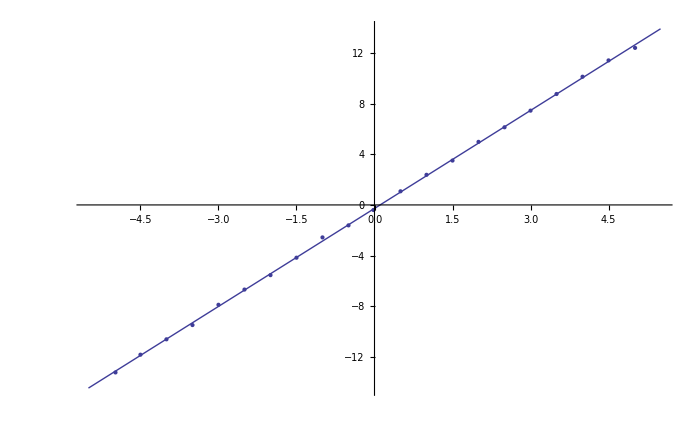

```mathematica
Show[Plot[Normal[fit],{x,-5.5,5.5}],ListPlot[data],ImageSize->700]
```

```mathematica
fit=LinearModelFit[data,x,x]
fit["ParameterTable"]
```

FittedModel[-0.276822+2.5764 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.276822 | 0.0261422 | -10.5891 | 2.07701×10^-9
x | 2.5764 | 0.00863672 | 298.308 | 2.42969×10^-36

-0.02 | 0.41833
1. | 0.287228
2. | 0.165831
3. | 0.110868
4. | 0.165202
5.01 | 0.332603
-1. | 0.149304
-2. | 0.0478714
-3. | 0.15
-4. | 0.254951
-4.98 | 0.0853913
-4.5 | 0.242813
-3.5 | 0.232737
-2.5 | 0.287228
-1.5 | 0.228674
-0.5 | 0.201556
0.5 | 0.15
1.5 | 0.212132
2.5 | 0.104083
3.5 | 0.122474
4.5 | 0.158114

FittedModel[0.19559-0.000765576 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.19559 | 0.0198982 | 9.82953 | 6.93753×10^-9
x | -0.000765576 | 0.00657387 | -0.116458 | 0.908512

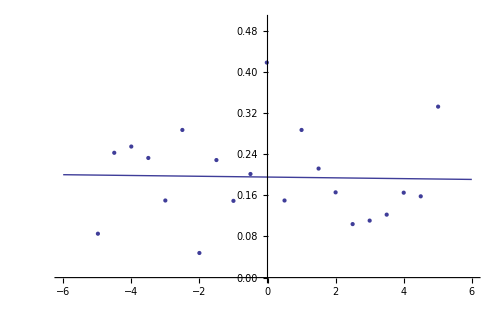

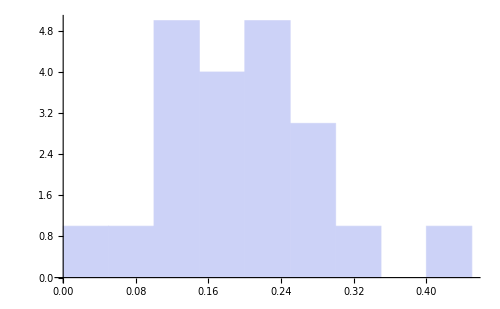

```mathematica
stabw=Table[{imp[[i,1]],StandardDeviation[Drop[imp[[i]],1]]},{i,1,Length[imp]}];
stabw//TableForm
fit2=LinearModelFit[stabw,x,x]
fit2["ParameterTable"]
Show[Plot[Normal[fit2],{x,-6,6},ImageSize->500,PlotRange->{0,0.5}],ListPlot[stabw]]
Histogram[stabw[[All,2]],{0.05}]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"\\data\\fara_data2.txt",Round[data,0.01],"Table"]
```

C:\fpgithub\0924-FarPock\data\fara_data2.txt